## Hexi — PS 4 — 2025-01-29

### Exercises from EIWL3 Section 11

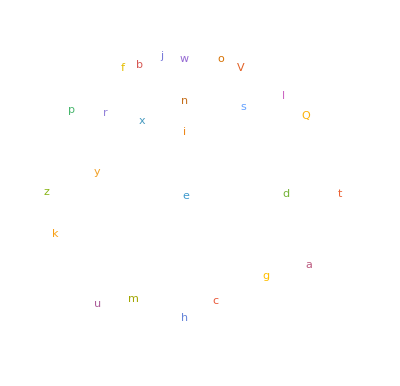

```mathematica
WordCloud[StringTake[StringReverse[WordList[]],1]]
```

```mathematica
RomanNumeral[1959]
```

MCMLIX

```mathematica
Max[StringLength[RomanNumeral[Range[1,2020]]]]
```

13

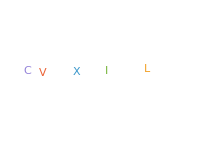

```mathematica
WordCloud[StringTake[RomanNumeral[Range[100]],1]]
```

```mathematica
Length[Alphabet["Russian"]]
```

33

```mathematica
ToUpperCase[Alphabet["Greek"]]
```

{Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω}

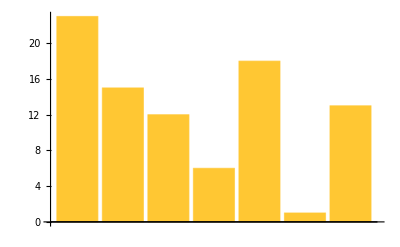

```mathematica
BarChart[LetterNumber["wolfram"]]
```

```mathematica
StringJoin[FromLetterNumber[RandomInteger[{1,26},1000]]]
```

nwohhcsrqjjjdewbtqudqnzomyycuyhhjwifbxuhnwdbgafzkehculinfrkhhquthhdyqgrmoncmukmmgllhwobvjhzzgdrvqsivazegvggshwdfoywhxspijiolzxtsnmqkfwmfemlcdegmcjqdadonhawurlskgnnuvkvtxihsdhaxhzoijtltxxhykemkltjceinwjmlsplstclemckuuywztsodjqydbtzowanlyccpxagoeodikykcinklwgvxlrxuhqqoartucaxvbaxfxgkvjgvepqlnddbvfzxvqatwftmadujoipfzaqrgclwshvhgvqsyarxlgmircbdxcpghfpulellrysgauvevmcimdbbjlepzjaolqzuxbtexchuhbiprzcstidfekglmheqsznzzokjzooqaizakjrbupyymyvbrhfxpikjnyvbvaixnqoqfwnswifwkstxgfhxblrufctqyhqkingavcouqkwwmkurxnrhvrgreomykqvmkiweuxxbftqqfqnmogldgnfjbcrwfqtmvssvwbneywcposaivinborsgjvojtscvpwdasetqyrgwjfeyjzqqqhllyxnmuofgdrayfvvwzcgqtcsxptpbivyplummyslxjvxnmgwhlqdczgstbdxlgsckbwmrgjtfwolxrbcunkikcagczqwfbgmqqbpnvhrfhijqlcizxjvnkbgdxhoyairnandtbtletttafxygjnmzuutsgijyglqnfktyzujovplnhxwoekoftwkzcopaghanwxnbkutenbgkeyonewdphehknwibluhgesjbslwivfarshjrugsmptqtwfyphvelvqzqagppqfpwfwzppfuachglbuybmjjicohxfvfaxsfxhkqpvszqnqkcwxoqbsgjdtyamzvmrhmnfkurycaqfeddktsvemrtvrwuicvkkipnyambusxgkvepwzeqaviuetpfnsqhdg

```mathematica
Table[StringJoin[FromLetterNumber[RandomInteger[{1,26},5]]],100]
```

{bwlre,kljla,hfpzy,urlvf,gnarv,pnnaj,zwdhy,xhvxn,oygcv,ismcq,ycuty,mgmgs,pzvon,hgrew,gbfhh,ncswm,tdcms,qtqoe,naqow,rscvk,khdxz,enwpy,jbvmj,brqxq,szdqa,chska,ffhrl,wwqqn,zfbhx,pulma,fytpc,jvodn,mgazn,ogofq,mjilh,btjcg,wifur,hdffr,cxktx,fpffw,bkmih,zxrgi,qpoqd,nuqmf,xkzzq,ugfhw,tvpsl,algdx,vsuur,oblfr,nbpaa,ardvv,ffwfh,nhjgp,sinyz,rlaxj,tjiod,zvnlg,hdvce,nqbqb,uxsbb,fhmcc,lvkbj,qajhw,bqhwz,zyhwm,glgas,ilbbc,awgmb,uazbe,usohx,itjzw,aujyw,hkgru,rstxl,zgwre,ulefw,dcoxu,zauuz,defzn,euhqf,jvzyw,kldwa,xyktp,pgldm,ifanx,wbkve,aeulo,serhr,pnibv,xzbkn,knrhd,fojvf,aermd,whuao,rtkty,jwore,oghgz,iwgat,htydk}

```mathematica
Transliterate["wolfram","Greek"]
```

βολφραμ

```mathematica
StringJoin[Table["🐺🐏",10]]
```

🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏

```mathematica
Transliterate[Alphabet["Arabic"]]
```

{a,b,t,th,j,h,kh,d,dh,r,z,s,sh,s,d,t,z,ʿ,gh,f,q,k,l,m,n,h,w,y}

```mathematica
Rasterize[Style["A",200,White, Background->Black]]
```

-Graphics-

```mathematica
Manipulate[Style[FromLetterNumber[x],100],{x,1,26,1}]
```

```mathematica
Manipulate[Rasterize[Style[c,100,Black, Background->White]],{{c,"a"},CharacterRange ["a","z"]}]
```

```mathematica
ManipulateBlur[Rasterize[Style["A",200]],x],{x,0,50}]
```

### Exercises from EIWL3 Section 12

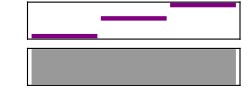

```mathematica
Sound[{SoundNote[0],SoundNote[4],SoundNote[7]}]
```

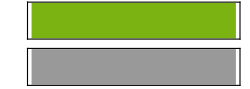

```mathematica
Sound[SoundNote["A",2,"Cello"]]
```

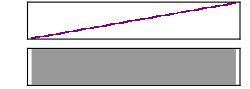

```mathematica
Sound[Table[SoundNote[x,0.05],{x,0,48,1}]]
```

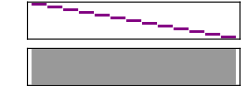

```mathematica
Sound[Reverse[Table[SoundNote[x],{x,0,12,1}]]]
```

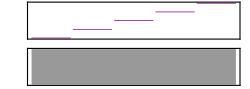

```mathematica
Sound[Table[SoundNote[x],{x,0,48,12}]]
```

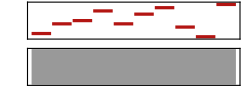

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.2,"Trumpet"],10]]
```

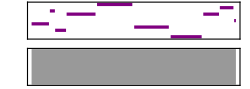

```mathematica
Sound[Table[SoundNote[RandomInteger[12],RandomReal[0.1]],10]]
```

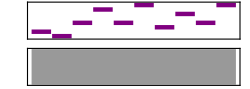

```mathematica
Sound[Table[SoundNote[x,0.1],{x,IntegerDigits[2^31]}]]
```

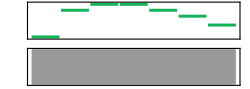

```mathematica
Sound[Table[SoundNote[x,0.3,"Guitar"],{x,Characters["CABBAGE"]}]]
```

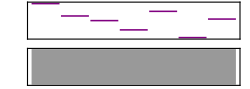

```mathematica
Sound[Table[SoundNote[x,0.1],{x,LetterNumber[Characters["wolfram"]]}]]
```

### Exercises from EIWL3 Section 13

```mathematica
Grid[Table[i*j,{i,12},{j,12}]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
Grid[RomanNumeral[Table[i*j,{i,5},{j,5}]]]
```

I | II | III | IV | V
II | IV | VI | VIII | X
III | VI | IX | XII | XV
IV | VIII | XII | XVI | XX
V | X | XV | XX | XXV

```mathematica
Grid[Table[RandomColor[],10,10]]
```

RGBColor[0.18697294912078988, 0.9719151338672865, 0.36240705628165104] | RGBColor[0.752870382634133, 0.18182479865839807, 0.2161177678565971] | RGBColor[0.40145189686369975, 0.5934207401180331, 0.679813131903112] | RGBColor[0.38017868576522207, 0.22432816648943987, 0.7671325698321285] | RGBColor[0.6202178085386512, 0.4534929333178175, 0.993238676478404] | RGBColor[0.9002299094402759, 0.5033503722149728, 0.5369127275536525] | RGBColor[0.6567754375700796, 0.9884303270399131, 0.25594627050832264] | RGBColor[0.49401434315857795, 0.6218482540882875, 0.37857361215593843] | RGBColor[0.7819326182927524, 0.2338257563792625, 0.6870638310585233] | RGBColor[0.6117739428715951, 0.5573595945697407, 0.28702496981340064]
RGBColor[0.7317523011999987, 0.37972649768708666, 0.6710237885848334] | RGBColor[0.05388017001511969, 0.07717907573874272, 0.9831684389585997] | RGBColor[0.7981071936339972, 0.2843883788705257, 0.9083710752402026] | RGBColor[0.9350162286402992, 0.20550587129239029, 0.742242914109269] | RGBColor[0.011309537680991744, 0.5395670943136526, 0.8603545883748003] | RGBColor[0.23747467584561122, 0.2846657790489895, 0.13915593547455707] | RGBColor[0.43578527842728243, 0.2556363101704473, 0.5162506550166257] | RGBColor[0.15559788208964598, 0.31323209346319314, 0.12316874163827718] | RGBColor[0.481112935930307, 0.9799241988908105, 0.783285947784996] | RGBColor[0.5930911494955768, 0.6916572717522407, 0.29841094301055415]
RGBColor[0.8535276373390255, 0.6295914132706459, 0.4794169925210905] | RGBColor[0.17493950758688204, 0.47503176320510865, 0.47329173169142913] | RGBColor[0.7448702899095792, 0.24549016205132945, 0.6211841339223196] | RGBColor[0.21868217468036133, 0.9212729782998716, 0.4222934203979811] | RGBColor[0.4605483768658556, 0.5543300840118579, 0.8977718741434539] | RGBColor[0.45865552778098584, 0.4246331421003424, 0.7798792591509658] | RGBColor[0.7677747779729747, 0.058867213666204954, 0.10543493691978134] | RGBColor[0.3204571393601021, 0.22056487254300072, 0.12023120321594805] | RGBColor[0.4574823960489045, 0.5409898595465599, 0.3465493867080731] | RGBColor[0.5279046424185356, 0.6338815629861985, 0.17454302812803868]
RGBColor[0.8958934627764974, 0.48840529110881503, 0.9678385796150397] | RGBColor[0.89131219374578, 0.007320207750301844, 0.8328556701411611] | RGBColor[0.6945695780642944, 0.7612670713502796, 0.26691273679022776] | RGBColor[0.3091095649573492, 0.25076773671244834, 0.09617057040494048] | RGBColor[0.0533232855935355, 0.08713144795018568, 0.8372926046832476] | RGBColor[0.13183597573284112, 0.2588547574797544, 0.388989226672255] | RGBColor[0.17355588901355135, 0.0968761760602832, 0.19949556333225238] | RGBColor[0.8361265454058078, 0.570860998882079, 0.7516622490173082] | RGBColor[0.7989364677877433, 0.11433610632874114, 0.3322724769817713] | RGBColor[0.03979015969769817, 0.8314421437907848, 0.2847813000355035]
RGBColor[0.31981278074571784, 0.5806324377509156, 0.2839528651929961] | RGBColor[0.8362661299466945, 0.8332396987168811, 0.5677172278892704] | RGBColor[0.38225591864774633, 0.0913284381645485, 0.5577417366066002] | RGBColor[0.9467874649949073, 0.5152452774132608, 0.07652964363318437] | RGBColor[0.03800380156035699, 0.7951717868019372, 0.5791543734988083] | RGBColor[0.2314505769046482, 0.18688160121051256, 0.3342348076911015] | RGBColor[0.9871980458327299, 0.39715058951524607, 0.468871443630678] | RGBColor[0.8229502866343927, 0.46689298879886465, 0.5076934550227228] | RGBColor[0.19651657333633943, 0.784746005631092, 0.2688818452984787] | RGBColor[0.4354722560253279, 0.27172079318007847, 0.33821005267932036]
RGBColor[0.37096116837611604, 0.8071907447105535, 0.8415256787872247] | RGBColor[0.4480136292530905, 0.8466655616077641, 0.38007686998512624] | RGBColor[0.6148409163092943, 0.13987156618978736, 0.3785241166400257] | RGBColor[0.41626666778170995, 0.4335760308084702, 0.8612640372677862] | RGBColor[0.13756129371559078, 0.6141484934926726, 0.6140240630862834] | RGBColor[0.30332898040847045, 0.12009982611014514, 0.18313390518950312] | RGBColor[0.028178630401173965, 0.49367337642957865, 0.8180203164067776] | RGBColor[0.26788904846159234, 0.3459096345961712, 0.8864370680198794] | RGBColor[0.36840464809379236, 0.5577389998116655, 0.6623446231123089] | RGBColor[0.6792694363432843, 0.48555725090983737, 0.7282366180580613]
RGBColor[0.05001087689033312, 0.7535522456625179, 0.5718335327906932] | RGBColor[0.432954036945675, 0.5080348755001547, 0.18315770975741796] | RGBColor[0.8740834547716767, 0.8601430424935819, 0.8245313049354241] | RGBColor[0.9883543353207083, 0.709984378414297, 0.14008513430135583] | RGBColor[0.6039947474786125, 0.6186167658736579, 0.24234659138449866] | RGBColor[0.8043418438228147, 0.9975172611743712, 0.2745892186751058] | RGBColor[0.19260484406352463, 0.7026815529075232, 0.9046289912288574] | RGBColor[0.32370578404339945, 0.8890747927709544, 0.11622435428413502] | RGBColor[0.07797565937917672, 0.3460334836923078, 0.9306516765633353] | RGBColor[0.6898513138319693, 0.6967326220616354, 0.7453756249885466]
RGBColor[0.4790712888436246, 0.08819649851938083, 0.7968883064163919] | RGBColor[0.3796274600934777, 0.3834057858135027, 0.17943826973746413] | RGBColor[0.4378391483181632, 0.2961271189155712, 0.05818285996666628] | RGBColor[0.9698085446090832, 0.3457191003013478, 0.6647811731421911] | RGBColor[0.8698030169204378, 0.5364737996111026, 0.9034114214019711] | RGBColor[0.9268545503131538, 0.6078218960702721, 0.6340702774964091] | RGBColor[0.9522287545092247, 0.19313179378785605, 0.023978991131073712] | RGBColor[0.4853820057149607, 0.8525206771894576, 0.7038116323916446] | RGBColor[0.8455009648438228, 0.9641188727783723, 0.47372004624850317] | RGBColor[0.19291196621358053, 0.9564223964339877, 0.17241239368377825]
RGBColor[0.5579729369879243, 0.5806600134696973, 0.058992045136822435] | RGBColor[0.8426853251929962, 0.8137543265153055, 0.11269208578608292] | RGBColor[0.48854421626976685, 0.1662168571933038, 0.5372445865981601] | RGBColor[0.18533184116369572, 0.04382913589072501, 0.939096526192152] | RGBColor[0.1947694313628141, 0.6277201303076827, 0.5089384922142424] | RGBColor[0.11015638879762224, 0.7102765412938294, 0.7398279472889011] | RGBColor[0.5824397577938369, 0.6827839449909616, 0.4195153577283406] | RGBColor[0.7645216892295894, 0.3848342494447281, 0.9872171287911844] | RGBColor[0.2058651654694239, 0.5826252850810907, 0.29399192031262866] | RGBColor[0.5915246367526892, 0.9772972144298799, 0.8783545883894532]
RGBColor[0.09800014307929583, 0.4482934104131402, 0.7241059725079748] | RGBColor[0.4540957247344466, 0.41406787159176983, 0.08021934662151109] | RGBColor[0.8109330105596988, 0.8776931134530528, 0.7856176238769121] | RGBColor[0.9818568059507933, 0.10405016540550904, 0.9075505349224173] | RGBColor[0.4965879275868337, 0.3567103590578644, 0.8924808187627029] | RGBColor[0.8645218701926838, 0.09654399705320316, 0.5307542268202627] | RGBColor[0.25313578237111, 0.5477681239520646, 0.44870781256611236] | RGBColor[0.7219723754888108, 0.16575862270116248, 0.8944700785427757] | RGBColor[0.03841240122851963, 0.5792190118215932, 0.1598992646970856] | RGBColor[0.22984119576770423, 0.0709674976796486, 0.9243599561133993]

```mathematica
Grid[Table[Style[RandomInteger[{1,10}],RandomColor[]],10,10]]
```

10 | 7 | 9 | 6 | 6 | 10 | 7 | 4 | 8 | 1
10 | 4 | 5 | 6 | 3 | 10 | 2 | 6 | 6 | 10
4 | 7 | 1 | 6 | 10 | 2 | 7 | 8 | 4 | 3
3 | 8 | 7 | 9 | 3 | 4 | 3 | 3 | 8 | 4
6 | 1 | 9 | 5 | 5 | 6 | 4 | 1 | 8 | 8
6 | 1 | 1 | 2 | 3 | 2 | 5 | 3 | 7 | 4
10 | 7 | 1 | 10 | 6 | 6 | 9 | 8 | 4 | 3
8 | 8 | 5 | 1 | 9 | 2 | 8 | 6 | 7 | 4
5 | 10 | 9 | 2 | 2 | 4 | 8 | 3 | 1 | 10
8 | 8 | 3 | 7 | 1 | 1 | 9 | 1 | 2 | 9

```mathematica
Table[a*b,{a,Alphabet[]},{b,Alphabet[]}]
```

{{a^2,a b,a c,a d,a e,a f,a g,a h,a i,a j,a k,a l,a m,a n,a o,a p,a q,a r,a s,a t,a u,a v,a w,a x,a y,a z},{a b,b^2,b c,b d,b e,b f,b g,b h,b i,b j,b k,b l,b m,b n,b o,b p,b q,b r,b s,b t,b u,b v,b w,b x,b y,b z},{a c,b c,c^2,c d,c e,c f,c g,c h,c i,c j,c k,c l,c m,c n,c o,c p,c q,c r,c s,c t,c u,c v,c w,c x,c y,c z},{a d,b d,c d,d^2,d e,d f,d g,d h,d i,d j,d k,d l,d m,d n,d o,d p,d q,d r,d s,d t,d u,d v,d w,d x,d y,d z},{a e,b e,c e,d e,e^2,e f,e g,e h,e i,e j,e k,e l,e m,e n,e o,e p,e q,e r,e s,e t,e u,e v,e w,e x,e y,e z},{a f,b f,c f,d f,e f,f^2,f g,f h,f i,f j,f k,f l,f m,f n,f o,f p,f q,f r,f s,f t,f u,f v,f w,f x,f y,f z},{a g,b g,c g,d g,e g,f g,g^2,g h,g i,g j,g k,g l,g m,g n,g o,g p,g q,g r,g s,g t,g u,g v,g w,g x,g y,g z},{a h,b h,c h,d h,e h,f h,g h,h^2,h i,h j,h k,h l,h m,h n,h o,h p,h q,h r,h s,h t,h u,h v,h w,h x,h y,h z},{a i,b i,c i,d i,e i,f i,g i,h i,i^2,i j,i k,i l,i m,i n,i o,i p,i q,i r,i s,i t,i u,i v,i w,i x,i y,i z},{a j,b j,c j,d j,e j,f j,g j,h j,i j,j^2,j k,j l,j m,j n,j o,j p,j q,j r,j s,j t,j u,j v,j w,j x,j y,j z},{a k,b k,c k,d k,e k,f k,g k,h k,i k,j k,k^2,k l,k m,k n,k o,k p,k q,k r,k s,k t,k u,k v,k w,k x,k y,k z},{a l,b l,c l,d l,e l,f l,g l,h l,i l,j l,k l,l^2,l m,l n,l o,l p,l q,l r,l s,l t,l u,l v,l w,l x,l y,l z},{a m,b m,c m,d m,e m,f m,g m,h m,i m,j m,k m,l m,m^2,m n,m o,m p,m q,m r,m s,m t,m u,m v,m w,m x,m y,m z},{a n,b n,c n,d n,e n,f n,g n,h n,i n,j n,k n,l n,m n,n^2,n o,n p,n q,n r,n s,n t,n u,n v,n w,n x,n y,n z},{a o,b o,c o,d o,e o,f o,g o,h o,i o,j o,k o,l o,m o,n o,o^2,o p,o q,o r,o s,o t,o u,o v,o w,o x,o y,o z},{a p,b p,c p,d p,e p,f p,g p,h p,i p,j p,k p,l p,m p,n p,o p,p^2,p q,p r,p s,p t,p u,p v,p w,p x,p y,p z},{a q,b q,c q,d q,e q,f q,g q,h q,i q,j q,k q,l q,m q,n q,o q,p q,q^2,q r,q s,q t,q u,q v,q w,q x,q y,q z},{a r,b r,c r,d r,e r,f r,g r,h r,i r,j r,k r,l r,m r,n r,o r,p r,q r,r^2,r s,r t,r u,r v,r w,r x,r y,r z},{a s,b s,c s,d s,e s,f s,g s,h s,i s,j s,k s,l s,m s,n s,o s,p s,q s,r s,s^2,s t,s u,s v,s w,s x,s y,s z},{a t,b t,c t,d t,e t,f t,g t,h t,i t,j t,k t,l t,m t,n t,o t,p t,q t,r t,s t,t^2,t u,t v,t w,t x,t y,t z},{a u,b u,c u,d u,e u,f u,g u,h u,i u,j u,k u,l u,m u,n u,o u,p u,q u,r u,s u,t u,u^2,u v,u w,u x,u y,u z},{a v,b v,c v,d v,e v,f v,g v,h v,i v,j v,k v,l v,m v,n v,o v,p v,q v,r v,s v,t v,u v,v^2,v w,v x,v y,v z},{a w,b w,c w,d w,e w,f w,g w,h w,i w,j w,k w,l w,m w,n w,o w,p w,q w,r w,s w,t w,u w,v w,w^2,w x,w y,w z},{a x,b x,c x,d x,e x,f x,g x,h x,i x,j x,k x,l x,m x,n x,o x,p x,q x,r x,s x,t x,u x,v x,w x,x^2,x y,x z},{a y,b y,c y,d y,e y,f y,g y,h y,i y,j y,k y,l y,m y,n y,o y,p y,q y,r y,s y,t y,u y,v y,w y,x y,y^2,y z},{a z,b z,c z,d z,e z,f z,g z,h z,i z,j z,k z,l z,m z,n z,o z,p z,q z,r z,s z,t z,u z,v z,w z,x z,y z,z^2}}

```mathematica
Grid[{{PieChart[{1,4,3,5,2}],NumberLinePlot[{1,4,3,5,2}]},{ListLinePlot[{1,4,3,5,2}],BarChart[{1,4,3,5,2}]}}]
```

-Graphics-

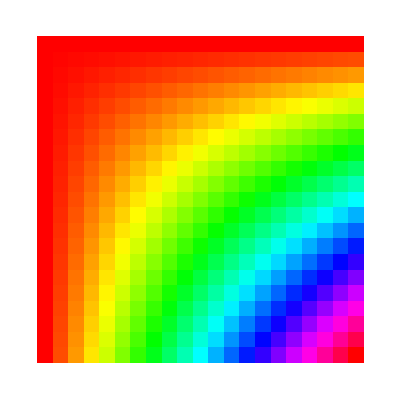

```mathematica
ArrayPlot[Table[Hue[x*y],{x,0,1,0.05},{y,0,1,0.05}]]
```

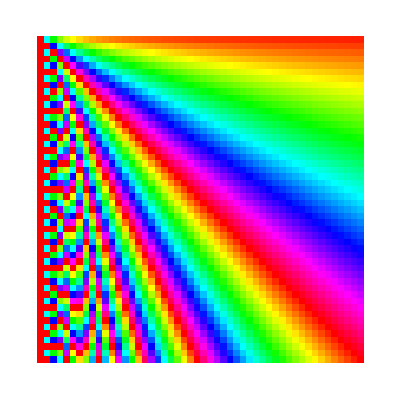

```mathematica
ArrayPlot[Table[Hue[x/y],{x,1,50,1},{y,1,50,1}]]
```

```mathematica
ArrayPlot[StringLength[RomanNumeral[Table[i*j,{i,100},{j,100}]]]]
```

-Graphics-